```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

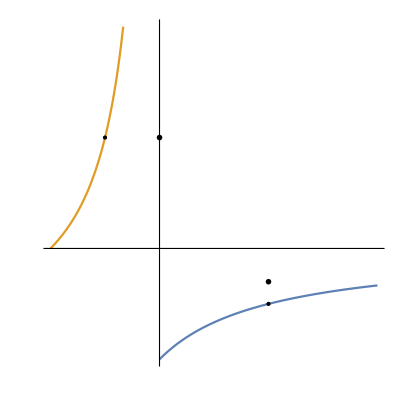

```mathematica
p1=ParametricPlot[{{x,-1/(x+1)},{-1/(x+1),x}},{x,0,2},BaseStyle->texStyle,

Frame->False, Ticks->None,Epilog->{PointSize[Medium],Point[{{1,-1/2},{-1/2,1}}],Inset[MaTeX["(f^{-1}(x),x)",Magnification->1.5],{1,-0.3}],Inset[MaTeX["(x,f^{-1}(x))",Magnification->1.5],{0,1}]}]
```

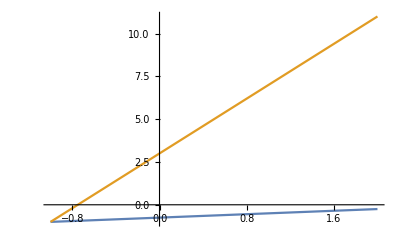

```mathematica
p2=Plot[{(x-1)/4-1/2,4(x+1/2)+1},{x,-1,2}]
```

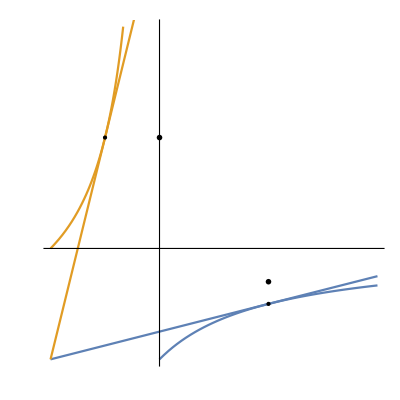

```mathematica
p3=Show[p1,p2]
```